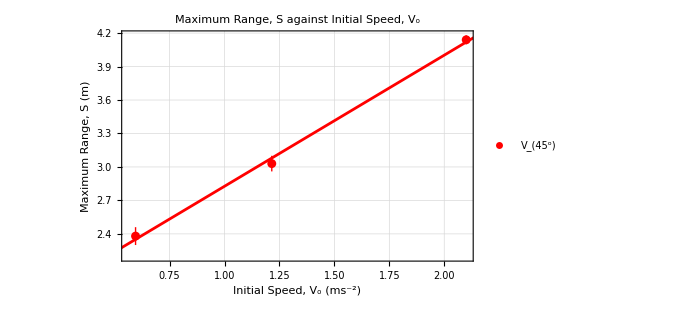
-Graphics-
V_(45^o): y==1.17523 x+1.65162

```mathematica
(*Define the data*)
V={{0.595,2.38},{1.215,3.03},{2.100,4.14}};

(*error bar*)
Verror={{Around[0.595,0.001],Around[2.38,0.08]},
{Around[1.215,0.001],Around[3.03,0.07]},
{Around[2.100,0.001],Around[4.14,0.04]}};

(*Extract x and y values for each set of data*)
x1=V[[All,1]];
y1=V[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fit1["BestFit"]]];

(*Display the equations outside the graph*)
Column[{Show[ListPlot[{Verror},PlotStyle->{Red},PlotLegends->{"V_(45^o)"}],Plot[{fit1[x]},{x,0,3},PlotStyle->{Red}],Frame->True,FrameLabel->{"Initial Speed, V_o (ms^-2)","Maximum Range, S (m)"},GridLines->Automatic,PlotLabel->"Maximum Range, S against Initial Speed, V_o",ImageSize->500],Column[{Row[{"V_(45^o): ",eq1}]}]}]
```